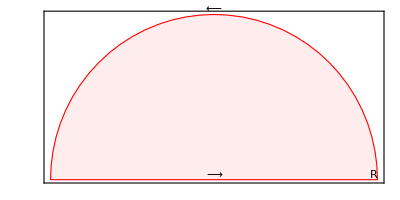

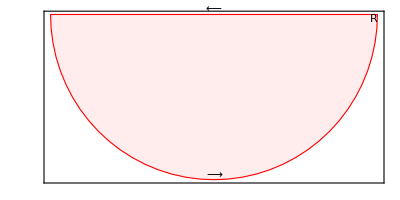

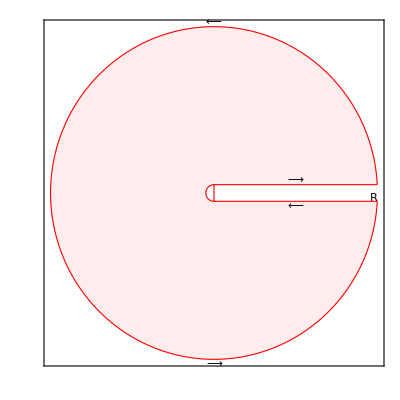

C:\Users\AllanStruthers\Desktop\GitHub\Spring_2026_Courses\Complex Analysis\Week 14

Pic1.png

Pic2.png

Pic3.png

```mathematica
{R,r}={20,1};
Pic1= Graphics[{EdgeForm[Red],
{LightPink, Disk[{0,0},R,{0, π}]},
Text["R",{R,0},{1,-1}],
Text["⟵",{0,R},{0,-1}],
Text["⟶",{0,0},{0,-1}]
},Axes->True, Frame->True,FrameTicks->None,AspectRatio->Automatic,PlotRangePadding->2]

Pic2= Graphics[{EdgeForm[Red],
{LightPink, Disk[{0,0},R,{π, 2π}]},
Text["R",{R,0},{1,1}],
Text["⟶",{0,-R},{0,-1}],
Text["⟵",{0,0},{0,-1}]
},Axes->True, Frame->True,FrameTicks->None,AspectRatio->Automatic,PlotRangePadding->2]

Pic3= Graphics[{EdgeForm[Red],
{LightPink, Disk[{0,0},R]},
{White,Disk[{0,0},r]},
{White, Rectangle[{0,-r},{R,r}]},
{White,Thick, Line[{{R,-r},{R,r}}]},
Text["R",{R,0},{1,1}],
Text["⟶",{0,-R},{0,1}],
Text["⟵",{R/2,-r},{0,1}],
Text["⟶",{R/2,r},{0,-1}],
Text["⟵",{0,R},{0,-1}]
},Axes->True, Frame->True,FrameTicks->None,AspectRatio->Automatic,PlotRangePadding->2]
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring_2026_Courses\\Complex Analysis\\Week 14"]
Export["Pic1.png",Pic1]
Export["Pic2.png",Pic2]
Export["Pic3.png",Pic3]
```